Sampling

### Logistic Function

```mathematica
Logistic[x_]:= 1/(1+Exp[-x])
```

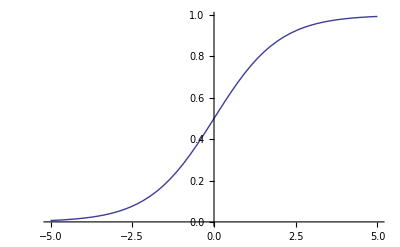

```mathematica
Plot[Logistic[x],{x,-5,5}]
```

### Main Functions

```mathematica
Weight[m_,n_]:=RandomReal[{-1,1},{m,n}]
Visibles[m_]:=RandomInteger[1,m]
Hiddens[n_]:=RandomInteger[1,n]
BiasHiddenSampling[n_]:=RandomInteger[0,n]
BiasVisibleSampling[m_]:=RandomInteger[0,m]
```

### Sampling Functions

```mathematica
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
zsample[l_]:= (Sign[Thread[l - RandomReal[1, Length[l]]]]+1)/2;
SampleHidden[w_][v_]:=sample[Logistic[wᵀ.v]];
SampleVisible[w_][h_]:= sample[Logistic[w.h]];
HiddenProbabilities[w_][v_]:=Logistic[wᵀ.v];
VisibleProbabilities[w_][h_]:= Most[Logistic[w.h]];
```

## Learning

```mathematica
DeltaWeight[ϵ_,v1_][w_]:=Module[{h1,v2,h2,w0,w1,wnew,v3,h3},
wnew=w;
Do[
h1=SampleHidden[w][v1];
v2=SampleVisible[w][h1];
h2=SampleHidden[w][v2];
v3=SampleVisible[w][h2];
h3=SampleHidden[w][v3];

(*
w0=1-Outer[BitXor, v1, h1];
w1=1-Outer[BitXor, v1, h3];*)
w0=Outer[Times, v1, h1];
w1=Outer[Times, v1, h3];

wnew += ϵ*(w0-w1);
,
{16}];
wnew
]
```

```mathematica
DataLearning[w_,ϵ_,n_,dataV_]:=Nest[Function[DeltaWeight[ϵ,RandomChoice[dataV]][#]],w,n]
```

```mathematica
StepLearning[w_,ϵ_,n_,dataV_]:=Monitor[time=0;Module[{w1,w2,w3},
w1=Nest[Function[time++;DeltaWeight[ϵ,RandomChoice[dataV]][#]],w,n/3];
w2=Nest[time++;Function[DeltaWeight[ϵ/10,RandomChoice[dataV]][#]],w1,n/3];
w3=Nest[time++;Function[DeltaWeight[ϵ/100,RandomChoice[dataV]][#]],w2,n/3];
w3
],time]
```

```mathematica
square[col_]:=Graphics[Style[Rectangle[],col],ImageSize->10,Frame->True,FrameTicks->False];
numbers2colors[x_]:= x /. {-1 -> square[White], 1->square[Black], r_Real  :> Tooltip[square[Blend[{Red,White,Blue}, r]],r]};
```

```mathematica
Stacking2Level[ϵ_,n_,vn_,hn1_,hn2_,data_]:=Module[{wr1,wr2,w1,w2,data1,data2,data21,up1,up11,up2,down1,down11,down2,Final},
wr1=RandomReal[{-0.5,0.5},{vn+1,hn1}];
data1=Append[2*#-1,1]&/@data; 
w1=StepLearning[wr1,ϵ,n,data1];
data21=SampleHidden[w1][#]&/@data1;
data2=Append[#,1]&/@data21;
wr2 =RandomReal[{-0.5,0.5},{hn1+1,hn2}];
w2=StepLearning[wr2,ϵ,n,data2];

up1=SampleHidden[w1][#]&/@data1;
up11=Append[#,1]&/@up1;
up2=SampleHidden[w2][#]&/@up11;
down1=SampleVisible[w2][#]&/@up2;
down11=Most[#]&/@down1;
down2=SampleVisible[w1][#]&/@down11;
Final=Most[#1]&/@Map[((#+1)/2)&,down2]

]
```

## Testing

```mathematica
data=Append[2*#-1,1]&/@{{1,1,1,1,0,0,0,0},{0,0,0,0,1,1,1,1}};
wcomp=StepLearning[RandomReal[{-1,1},{9,10}],0.02,1800,data];
```

```mathematica
wcomp
```

```mathematica
N[677/(231*20)]
```

0.146537

```mathematica
N[15/91]
```

0.164835

```mathematica
b=Flatten/@Table[CellularAutomaton[i,{0,0,0,1,0,0,0},64],{i,20}];
```

```mathematica
a==b
```

False

```mathematica
a=Partition[Flatten[Table[CellularAutomaton[i,{0,0,0,1,0,0,0},32],{i,10}]],231]//Dimensions
```

{10,231}

```mathematica
Table[CellularAutomaton[i,{0,0,0,1,0,0,0},32],{i,30,45,54,67}]
```

Table::itraw: Raw object 30 cannot be used as an iterator.

Table[CellularAutomaton[i,{0,0,0,1,0,0,0},32],{30,45,54,67}]

```mathematica
CellularAutomaton[226,{0,0,0,1,0,0,0},32]
```

{{0,0,0,1,0,0,0},{0,0,1,0,0,0,0},{0,1,0,0,0,0,0},{1,0,0,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,1,0,0},{0,0,0,1,0,0,0},{0,0,1,0,0,0,0},{0,1,0,0,0,0,0},{1,0,0,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,1,0,0},{0,0,0,1,0,0,0},{0,0,1,0,0,0,0},{0,1,0,0,0,0,0},{1,0,0,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,1,0,0},{0,0,0,1,0,0,0},{0,0,1,0,0,0,0},{0,1,0,0,0,0,0},{1,0,0,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,1,0,0},{0,0,0,1,0,0,0},{0,0,1,0,0,0,0},{0,1,0,0,0,0,0},{1,0,0,0,0,0,0},{0,0,0,0,0,0,1}}